# Exercise 3.2

### task a)

```mathematica
ClearAll["Global`*"]
a= 4/9;
b = 5/9;
ϵ = 1;

xdot[x_,y_,current_] := (1/ϵ)*(x-(1/3)*x^3-y+current)
ydot[x_,y_] := x+a-b*y

jacobi[x_,y_,current_] = D[{xdot[x,y,current],ydot[x,y]},{{x,y}}];

sol[x_,y_,current_] = Solve[{xdot[x,y,current] == 0,ydot[x,y] == 0}, {x,y}];

stabilityMatrix[current_]=jacobi[x,y,current]/. sol[x,y,current][[1]];

τ[current_] = Tr[stabilityMatrix[current]];
Δ [current_]= Det[stabilityMatrix[current]];

ic = Solve[τ[current] == 0, current]

(*If trace = τ == 0, potential Hopf bif occur. trace = 0 indicate that the real part of the eigen values are zero*)
(*Choose I such that: 0 <= I <= 1*)
```

{{current→68/405},{current→116/81}}

### task b)

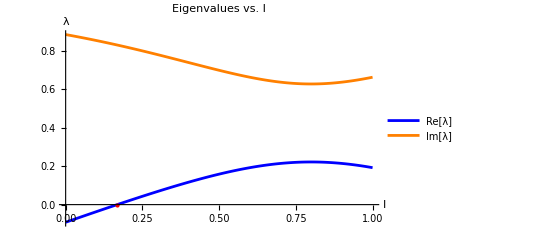

```mathematica
ivals = Table[i,{i,0,1,0.01}];
evs = Table[{0,0},{i,Length[ivals]}];
Do[
sol= NSolve[{xdot[x,y,ivals[[j]]] == 0, ydot[x,y] == 0}, {x,y}, Reals];
fpx = x/. sol[[1]];
fpy = y /. sol[[1]];
jacobi=D[{xdot[x , y , ivals[[j]]],ydot[x,y]},{{x,y}}]/. {x->fpx,y->fpy};
eig = Eigenvalues[jacobi][[1]];
evs[[j]] = eig; 
, {j, Length[ivals]}];

dataRe = Transpose@{ivals, Re[evs]}; 
dataIm = Transpose@{ivals, Im[evs]};

realPlot=ListLinePlot[dataRe,
PlotStyle->Blue,
PlotRange->All,
PlotLegends->{"Re[λ]"}];

imaginaryPlot=ListLinePlot[dataIm,
PlotStyle->Orange,
PlotRange->All,
PlotLegends->{"Im[λ]"}];

Show[realPlot,imaginaryPlot,
PlotLabel->"Eigenvalues vs. I",
PlotRange->Full,
AxesLabel -> {"I","λ"},
PlotLegends->{"Real Part","Imaginary Part"},
Epilog->{Red,PointSize[Large],Point[{current /. ic[[1]],0}]}]
```

### Task c)

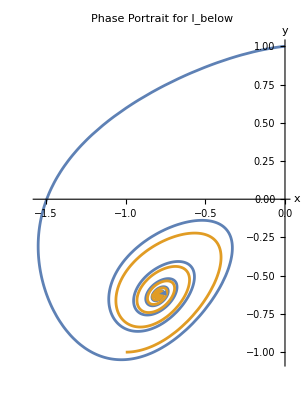

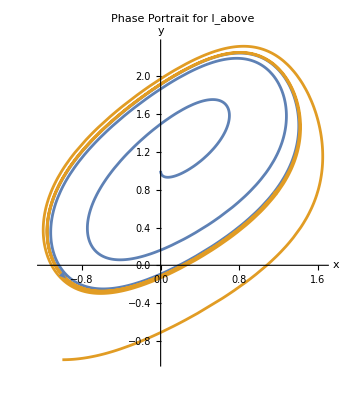

```mathematica
ClearAll["Global`*"]
ic=68/405;
icAbove=1;
icBelow= 0;
a= 4/9;
b = 5/9;
ϵ = 1;

f[x_,y_,current_]:=(1/ϵ)*(x-(1/3)*x^3-y+current)
g[x_,y_,current_]:=x+a-b*y

(*Define a range of initial conditions*)
initialConditions={{0,1},{-1,-1} };

(*Solve the System Numerically for Ibelow with multiple initial conditions*)
trajectoriesBelow=Table[NDSolve[{
x'[t]==f[x[t],y[t],icBelow],
y'[t]==g[x[t],y[t],icBelow],
x[0]==init[[1]],
y[0]==init[[2]]},
{x,y},{t,0,50}],
{init,initialConditions}];

(*Solve the System Numerically for Iabove with multiple initial conditions*)
trajectoriesAbove=Table[NDSolve[{
x'[t]==f[x[t],y[t],icAbove],
y'[t]==g[x[t],y[t],icAbove],
x[0]==init[[1]],
y[0]==init[[2]]},
{x,y},{t,0,50}],
{init,initialConditions}];

(*Phase Portrait for Ibelow*)
ParametricPlot[Evaluate[Table[{x[t],y[t]}/. sol,{sol,trajectoriesBelow}]],{t,0,50},
PlotRange->All,
AxesLabel->{"x","y"},
PlotLabel->"Phase Portrait for I_below"
]/. Line[x_]:>{Arrowheads[{{0.05,0.2},{0.05,0.5},{0.05,0.75}}],Arrow[x]}

(*Phase Portrait for Iabove*)
ParametricPlot[Evaluate[Table[{x[t],y[t]}/. sol,{sol,trajectoriesAbove}]],{t,0,25},
PlotRange->All,
AxesLabel->{"x","y"},
PlotLabel->"Phase Portrait for I_above"]/. Line[x_]:>{Arrowheads[{{0.05,0.1},{0.05,0.5},{0.05,0.75}}],Arrow[x]}
```

We see that the stability of the spiral has changed over the different values of I => Hopf bifurcation.

### Task d)

{{x→-1.39248,y→-0.392477}}

{-1.39248,-0.392477}

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

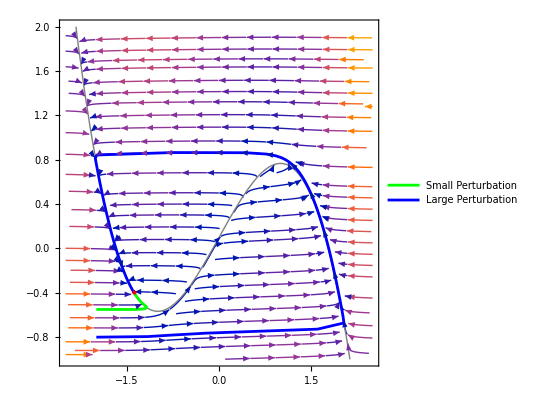

```mathematica
ClearAll["Global`*"]
a = 1;
b= 1;
ϵ = 0.01; 
IBelow = 0.1;

f[x_,y_,current_]:=(1/ϵ)*(x-(1/3)*x^3-y+current)
g[x_,y_,current_]:=x+a-b*y

initialConditions={{-2,-0.55},{-2,-0.8} };

trajectoriesBelow=Table[NDSolve[{
x'[t]==f[x[t],y[t],IBelow],
y'[t]==g[x[t],y[t],IBelow],
x[0]==init[[1]],
y[0]==init[[2]]},
{x,y},{t,0,50}],
{init,initialConditions}];

nullclineX[x_,current_] :=  NSolve[f[x,y,current]==0,y,Reals]

fp = NSolve[{f[x,y,IBelow]==0,g[x,y,IBelow] == 0}, {x,y},Reals]
fixedPoint = {x,y} /. fp[[1]]

pbelow = ParametricPlot[Evaluate[Table[{x[t],y[t]}/. sol,{sol,trajectoriesBelow}]],{t,0,50},
PlotRange->All,
AxesLabel->{"x","y"},
PlotLabel->"Phase Portrait for I_below",
PlotStyle-> {Green,Blue},
PlotLegends->{"Small Perturbation","Large Perturbation"}
]/. Line[x_]:>{Arrowheads[{{0.03,0.2},{0.03,0.5},{0.03,0.75}}],Arrow[x]};

nullcline = Plot[
Evaluate[y/. nullclineX[x,IBelow]],{x,-2.5,2.5},
PlotRange->{-1,2},
AxesLabel->{"x","y"},
PlotStyle->{Gray,Thick},
PlotLegends->"Expressions"
];

splot = StreamPlot[{f[x,y,IBelow],g[x,y,IBelow]},{x,-2.5,2.5},{y,-1,2},
StreamStyle->Gray,
StreamPoints->Fine
];

Show[
splot,nullcline,pbelow,
Epilog->{Red,PointSize[Large],Point[fixedPoint] }
]
```

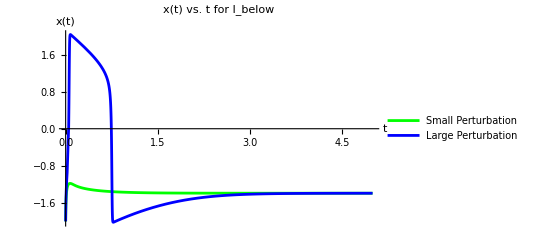

```mathematica
Plot[Evaluate[Table[x[t]/. sol[[1]],{sol,trajectoriesBelow}]],{t,0,5},
PlotRange-> All,
AxesLabel->{"t","x(t)"},
PlotLabel->"x(t) vs. t for I_below",
PlotStyle->{Green,Blue},
PlotLegends->{"Small Perturbation","Large Perturbation"}]
```

Both have converged to the FP at approx. t = 4. We can see the fast and slow parts of the trajectory.

### task e)

```mathematica
ClearAll["Globla`*"]
f[x_]=1+x-(1/3)x^3
fPrime[x_] = D[f[x],x] 

(*Derivation of integrand with pen and paper.*)

Tslow=Integrate[(3/x^3)*fPrime[x],{x,2,1}]  // Simplify
```

1+x-x^3/3

1-x^2

-9/8+Log[8]